```mathematica
len:=5
A[r_]:=f''[r]/2
B[r_]:=-f'[r]/(2*r)
ψ[r_]:=(1-f[r])/r^2
```

```mathematica
Z[n_]=Expand[-4*n*(n-1)*(B[r]^2)*(ψ[r]^(n-2))+n*(2*A[r]-4*(len-2*n)*B[r])*ψ[r]^(n-1)-(len-2*n)*(len-2*n-1)*ψ[r]^n]
```

-20 ((1-f[r])/r^2)^n+18 n ((1-f[r])/r^2)^n-4 n^2 ((1-f[r])/r^2)^n+(10 n ((1-f[r])/r^2)^(-1+n) f'[r])/r-(4 n^2 ((1-f[r])/r^2)^(-1+n) f'[r])/r+(n ((1-f[r])/r^2)^(-2+n) f'[r]^2)/r^2-(n^2 ((1-f[r])/r^2)^(-2+n) f'[r]^2)/r^2+n ((1-f[r])/r^2)^(-1+n) f''[r]

```mathematica
Z1=Simplify[Z[1]]
```

(-6+6 f[r]+6 r f'[r]+r^2 f''[r])/r^2

```mathematica
Z2=Expand[Simplify[Z[2]*r^3]]
```

4 f'[r]-4 f[r] f'[r]-2 r f'[r]^2+2 r f''[r]-2 r f[r] f''[r]

```mathematica
Z3=Expand[Simplify[Z[3]]]
```

-2/r^6+(6 f[r])/r^6-(6 f[r]^2)/r^6+(2 f[r]^3)/r^6-(6 f'[r])/r^5+(12 f[r] f'[r])/r^5-(6 f[r]^2 f'[r])/r^5-(6 f'[r]^2)/r^4+(6 f[r] f'[r]^2)/r^4+(3 f''[r])/r^4-(6 f[r] f''[r])/r^4+(3 f[r]^2 f''[r])/r^4

```mathematica
FZ[n_]:=((len-2*n)/2)*((1-f[r])^n)*r^(len-2*n-1)
```

```mathematica
FZ[3]==μ
```

-(1-f[r])^3/(2 r^2)==μ

```mathematica
Solve[FZ[3]==μ,f[r],r]
```

Solve::bdomv: Warning: r is not a valid domain specification. Assuming it is a variable to eliminate.

{{f[r]→1+2^(1/3) r^(2/3) μ^(1/3)},{f[r]→1-((1-ⅈ √3) r^(2/3) μ^(1/3))/2^(2/3)},{f[r]→1-((1+ⅈ √3) r^(2/3) μ^(1/3))/2^(2/3)}}

```mathematica
Solve[FZ[4]]
```

-(3 (1-f[r])^4)/(2 r^4)

```mathematica
solucionesFZ[i_]:=Solve[FZ[i]==μ,f[r],r]
```

```mathematica
solucionesFZ[4]
```

Solve::bdomv: Warning: r is not a valid domain specification. Assuming it is a variable to eliminate.

```mathematica
μ=4
```

4

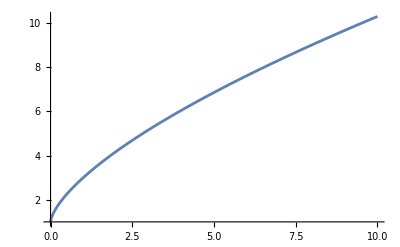

```mathematica
Plot[1+2^(1/3) r^(2/3) μ^(1/3),{r,0,10}]
```